```mathematica
ClearAll["Global`*"]
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/2015-2016 Fall/PH 4433 Computational Physics/Homework/Homework 5/ohg6-hw5/";
(*~ Windows ~*)
(*main="/Users/Mikhail/Box Sync/Education/MSU/2015-2016 Fall/PH 4433 Computational Physics/Homework/Homework 4/ohg6-hw4/";*)

SetDirectory[main];
$Line=0;
```

```mathematica
data=Import["data/data.txt","Table"];
```

```mathematica
Dynamic[Refresh[ListPlot[Import["data/data.txt","Table"]],UpdateInterval->1]]
```

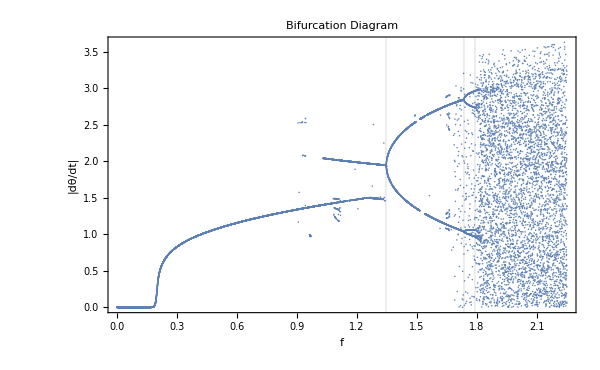

bifurcation.png

```mathematica
ListPlot[data,PlotStyle->PointSize[0.0018],Frame->True,FrameTicks->{{True,None},{True,None}},Axes->False,PlotLabel->"Bifurcation Diagram",FrameLabel->{"f","|dθ/dt|"},LabelStyle->{FontFamily->Times,FontSize->18},GridLines->{{1.345,1.735,1.79},None},ImageSize->600,Epilog->Inset[ListPlot[data,PlotRange->{{1,1.5},{1,2.75}},Axes->False,Frame->True,FrameTicks->{{None,None},{None,None}}],{1/2,3}]]
Export["bifurcation.png",%,ImageResolution->100]
```

```mathematica
(1.735-1.345)/(1.79-1.735)
```

7.09091